```mathematica
mesh = Import["/home/rationalash/Documents/BOLT/volume-calc/brain-gear.stl"]
R = RegionIntersection[Polygon[{{1,1,0},{1,-1,0},{-1,-1,0},{-1,1,0}}], mesh]
```

-Graphics3D-

RegionIntersection::reg: … is not a correctly specified region.

RegionIntersection[Polygon[{{1,1,0},{1,-1,0},{-1,-1,0},{-1,1,0}}],-Graphics3D-]

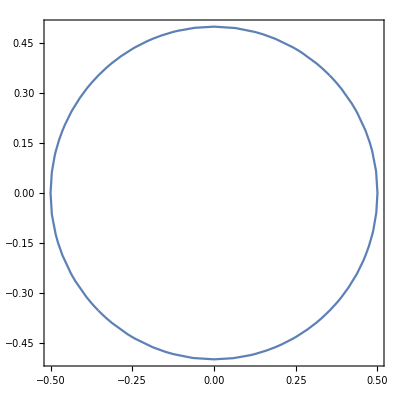

```mathematica
RegionPlot[DiscretizeRegion[R]]
```